```mathematica
(* Invert sin(x)+x *)
f[x_]:=Sin[x]+x;
g1=Limit[x/f[x],x->0];
g2=Limit[D[(x/f[x])^2,{x,1}],x->0];
g3=Limit[D[(x/f[x])^3,{x,2}],x->0];
g4=Limit[D[(x/f[x])^4,{x,3}],x->0];
g5=Limit[D[(x/f[x])^5,{x,4}],x->0];
g7=Limit[D[(x/f[x])^7,{x,6}],x->0];
{g1, g2, g3,g4,g5,g7}
```

{1/2,0,1/16,0,1/16,43/256}

1/2

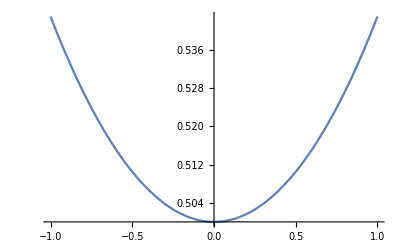

-Graphics-

```mathematica
Plot[D[(x/f[x])^1,{x,0}]/.x->y,{y,-1,1}]
Plot[x/f[x],{x,-1,1}]
```

```mathematica
(* Invert sin(x)+x *)
f[x_]:=Sin[x]+x;

For[i=0,i<8,i++,
n=2i+1;
Print[n,"   ",Limit[D[(x/f[x])^n,{x,n-1}],x->0]]
]
```

1   1/2

3   1/16

5   1/16

7   43/256

9   223/256

11   60623/8192

13   764783/8192

15   107351407/65536